0.422232

-0.000163304

-0.460102

0.00264097

0.437105

0.00364737

-0.398395

0.00315867

0.348811

0.0015107

-0.291728

0.0019927

0.231163

0.119109-0.0000797907 Cos[θ]-0.145112 (-1+3 Cos[θ]^2)+0.000985547 (-3 Cos[θ]+5 Cos[θ]^3)+0.0462394 (3-30 Cos[θ]^2+35 Cos[θ]^4)+0.000426561 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)-0.0253257 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)+0.000215687 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)+0.00316957 (35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8)+0.0000145124 (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9)-0.00147314 (-63+3465 Cos[θ]^2-30030 Cos[θ]^4+90090 Cos[θ]^6-109395 Cos[θ]^8+46189 Cos[θ]^10)+0.0000105308 (-693 Cos[θ]+15015 Cos[θ]^3-90090 Cos[θ]^5+218790 Cos[θ]^7-230945 Cos[θ]^9+88179 Cos[θ]^11)+0.000318408 (231-18018 Cos[θ]^2+225225 Cos[θ]^4-1021020 Cos[θ]^6+2078505 Cos[θ]^8-1939938 Cos[θ]^10+676039 Cos[θ]^12)

-Graphics3D-

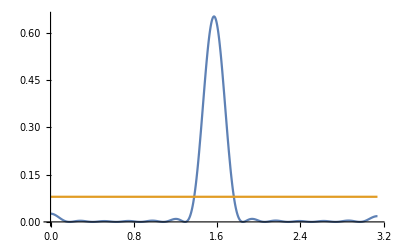

```mathematica
m1Y00=0.422232
m1Y01=-0.000163304
m1Y02=-0.460102
m1Y03=0.00264097
m1Y04=0.437105
m1Y05=0.00364737
m1Y06=-0.398395
m1Y07=0.00315867
m1Y08=0.348811
m1Y09=0.0015107
m1Y010=-0.291728
m1Y011=0.0019927
m1Y012=0.231163
m1[θ_]=m1Y00*SphericalHarmonicY[0,0,θ,0]+m1Y01*SphericalHarmonicY[1,0,θ,0]+m1Y02*SphericalHarmonicY[2,0,θ,0]+m1Y03*SphericalHarmonicY[3,0,θ,0]+m1Y04*SphericalHarmonicY[4,0,θ,0]+m1Y05*SphericalHarmonicY[5,0,θ,0]+m1Y06*SphericalHarmonicY[6,0,θ,0]+m1Y07*SphericalHarmonicY[7,0,θ,0]+m1Y08*SphericalHarmonicY[8,0,θ,0]+m1Y09*SphericalHarmonicY[9,0,θ,0]+
m1Y010*SphericalHarmonicY[10,0,θ,0]+m1Y011*SphericalHarmonicY[11,0,θ,0]+m1Y012*SphericalHarmonicY[12,0,θ,0]

SphericalPlot3D[{(m1[θ])^2, 1/(4 π)},{θ,0,π},{ϕ,0,π}, PlotRange -> All]
Plot[{(m1[θ])^2, 1/(4 π)},{θ,0,π}, PlotRange -> All]
```

```mathematica
N[Integrate[Sin[θ](m1[θ])^2 , {θ,80*π/180,100*π/180},{ϕ,0,2 Pi}]]
N[Integrate[Sin[θ](m1[θ])^2 , {θ,0,π},{ϕ,0,2 Pi}]]
```

Information::notfound: Symbol Delta not found.

```mathematica
SphericalPlot3D[{ (1/NConst)*SphericalHarmonicY[0,0,θ,ϕ]+(2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi}, PlotRange -> All]
```

-Graphics3D-

```mathematica
SphericalPlot3D[{ (2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi/2}, PlotRange -> All]
```

-Graphics3D-

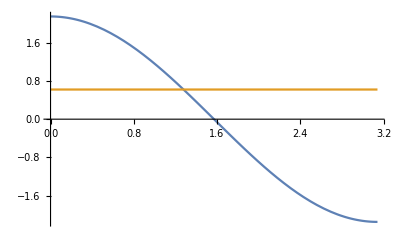

1.

```mathematica
Plot[{(2/NConst)*SphericalHarmonicY[1,0,θ,0] , (3/(4 Pi))^(1/3) },{θ,0,Pi}, PlotRange -> All]
```

```mathematica
N[m1[π/1.001]^2 * Sin[π/1.001]]
```

0.000382591